```mathematica
Clear["Global`*"]
r=0.1;
x=r*Cos[t];
y=r*Sin[t];
Index[p_,q_]:=1/(2π)Integrate[(p D[q,t]-q D[p,t])/(p^2+q^2),{t,0,2π}];
a=3;
```

Problem 1

1

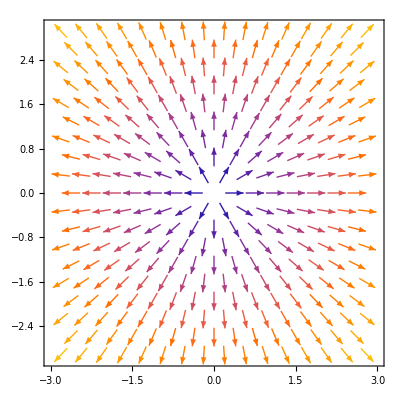

```mathematica
(* f(x,y) = (x,y) *)
p1=x;
q1=y;
Index[p1,q1]
VectorPlot[{x,y},{x,-a,a},{y,-a,a},Axes->True]
```

Having an index of 1 indicates that f(x,y) is stable, unstable, node, or a focus. Further analysis shows that the origin is an unstable equilibrium.

Problem 2

1

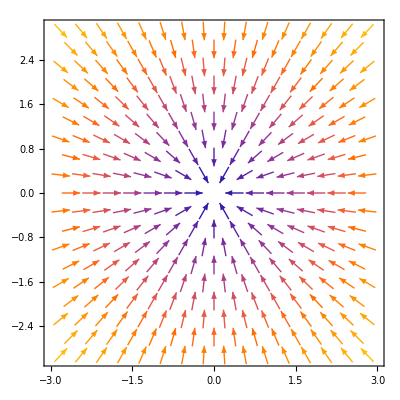

```mathematica
(* f(x,y) = (-x,-y) *)
p2=-x;
q2=-y;
Index[p2,q2]
VectorPlot[{-x,-y},{x,-a,a},{y,-a,a},Axes->True]
```

Having an index of 1 indicates that f(x,y) is stable, unstable, node, or a focus. Further analysis shows that the origin is a stable equilibrium.

Problem 3

1

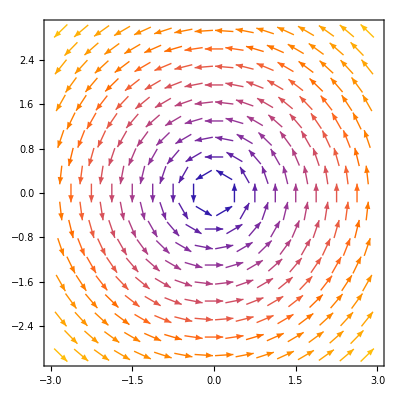

```mathematica
(* f(x,y) = (-y,x) *)
p3=-y;
q3=x;
Index[p3,q3]
VectorPlot[{-y,x},{x,-a,a},{y,-a,a},Axes->True]
```

Having an index of 1 indicates that f(x,y) is stable, unstable, node, or a focus. Further analysis shows that the origin is a center.

Problem 4

-1.

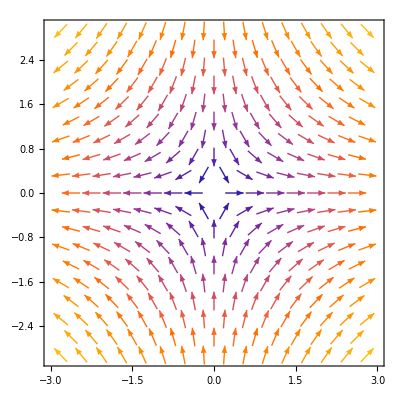

```mathematica
(* f(x,y) = (x,-y) *)
p4=x;
q4=-y;
Index[p4,q4]
VectorPlot[{x,-y},{x,-a,a},{y,-a,a},Axes->True]
```

Having an index of -1 indicates that f(x,y) is a saddle. Further analysis shows that the origin is in fact a saddle.